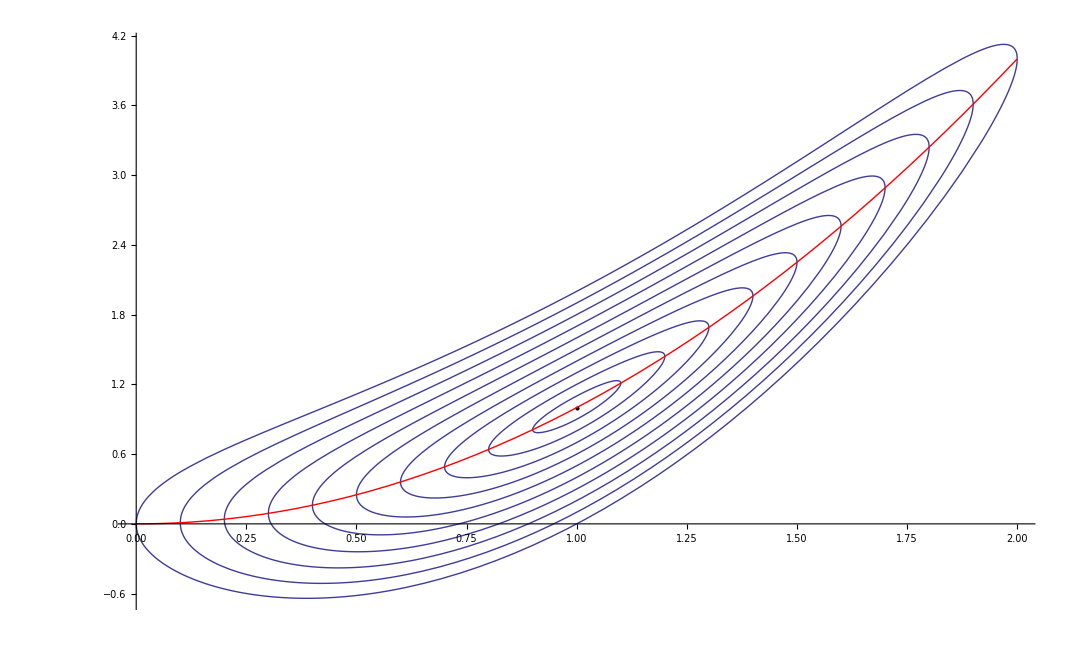

-Graphics3D-

```mathematica
α=1;
f[x_,y_]:=α^2 (x^2-y)^2+(x-1)^2;
Ypos[x_,c_]:=x^2+(√(c^2-(x-1)^2))/α;  Yneg[x_,c_]:=x^2-(√(c^2-(x-1)^2))/α;
c=0.0; Δc=0.1;
For[i=1,i≤10,i++,
c+=Δc;
Pos[i]=Plot[Ypos[x,i Δc],{x,1-c,1+c},PlotRange->All,AxesOrigin->{0,0}];
Neg[i]=Plot[Yneg[x,i Δc],{x,1-c,1+c},PlotRange->All,AxesOrigin->{0,0}];
];

ParPos=Plot[x^2+1,{x,1-α,1+α},PlotStyle->Red,PlotRange->{{-2,2},{-2,2}}];
ParNeg=Plot[x^2-1,{x,1-α,1+α},PlotStyle->Red,PlotRange->{{-2,2},{-2,2}}];

Show[Table[Pos[i],{i,1,10}],Table[Neg[i],{i,1,10}],Graphics[Point[{1,1}]],Plot[x^2,{x,0,2},PlotStyle->Red]]

Show[Plot3D[f[x,y],{x,-4,4},{y,-4,4},PlotRange->{{-4,4},{-4,4},{-1,10}}],Graphics3D[Sphere[{1,1,0},0.1]]]
```

```mathematica
?Point
```

Point[coords] is a graphics primitive that represents a point. 
Point[{coords_1,coords_2,…}] represents a collection of points.

```mathematica
?Sphere
```

Sphere[{x,y,z},r] represents a sphere of radius r centered at (x,y,z). 
Sphere[{x,y,z}] represents a sphere of radius 1. 
Sphere[{{x_1,y_1,z_1},{x_2,y_2,z_2},…},r] represents a collection of spheres of radius r.